Build dictionary (parsing the training dataset):

```mathematica
voc={"Set","List"}
```

{Set,List}

This will be used in pre- and post- processing:

```mathematica
encoder=NetEncoder[{"Tokens",voc,"IgnoreCase"->False}]
```

NetEncoder[<>]

```mathematica
decoder=NetDecoder[encoder]
```

NetDecoder[<>]

The language model is a RNN:

```mathematica
languagemodel=NetChain[{EmbeddingLayer[128],GatedRecurrentLayer[128],GatedRecurrentLayer[128],NetMapOperator[LinearLayer[]],SoftmaxLayer[]},"Input"->encoder,"Output"->decoder]
```

NetChain[<>]

It’s wrapped in a net to train:

```mathematica
trainingnet=NetGraph[<|"rest"->SequenceRestLayer[],"most"->SequenceMostLayer[],"net"->languagemodel,"loss"->CrossEntropyLossLayer["Index"]|>,{"net"->"most"->NetPort["loss","Input"],"rest" -> NetPort["loss","Target"]},"Input"->encoder]
```

NetGraph[<>]

```mathematica
TextElement
```

Train!
(Note: Use TextElement to trick NetEncoder[“Tokens”] and pass an explicit tokenization to it)

```mathematica
TextElement/@{{"Set","List"},{"List","Set"}}
```

{Set | List,List | Set}

```mathematica
trained=NetTrain[trainingnet,<|"Input"-> TextElement/@{{"Set","List"},{"List","Set"}}|>]
```

NetGraph[<>]

Extract the trained language model and do some obscure surgery:

```mathematica
trainedlanguagemodel=NetFlatten@NetTake[trained,{All,"net"}];
trainedlanguagemodel=NetReplacePart[NetAppend[trainedlanguagemodel,"next"->SequenceLastLayer[]],"Output"->NetDecoder[{"Class",Append[voc,_]}]]
```

NetChain[<>]

Demo of predicting the next symbol:

```mathematica
trainedlanguagemodel["Set"]
```

List

Demo of embeddings:

```mathematica
embedding=NetTake[trainedlanguagemodel,"net/1"]
```

NetChain[<>]

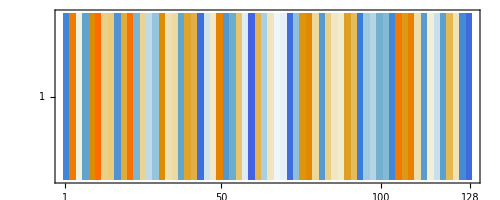

```mathematica
embedding["List"]//MatrixPlot
```

```mathematica
First@*embedding//Hold//FullForm
```

Hold[Composition[First,embedding]]

```mathematica
FeatureSpacePlot[{"List","Set"},FeatureExtractor->First@*embedding]
```

-Graphics-